Q1 a)

```mathematica
<<Notation`
```

```mathematica
Symbolize[Subscript[x, t+Δt]]
```

```mathematica
Symbolize[Subscript[ẋ, t+Δt]]
```

```mathematica
Symbolize[Subscript[x^(..), t+Δt]]
```

```mathematica
Symbolize[Subscript[x, t+γΔt]]
```

```mathematica
Symbolize[Subscript[ẋ, t+γΔt]]
```

```mathematica
Symbolize[Subscript[x^(..), t+γΔt]]
```

```mathematica
Symbolize[Subscript[x, t]]
```

```mathematica
Symbolize[Subscript[ẋ, t]]
```

```mathematica
Symbolize[Subscript[x^(..), t]]
```

```mathematica
Symbolize[Subscript[r, t+Δt]]
```

```mathematica
Symbolize[Subscript[r, t+γΔt]]
```

```mathematica
Symbolize[Subscript[Ω, o]]
```

```mathematica
Symbolize[Subscript[Ω̄, d]]
```

```mathematica
Symbolize[ξ̄]
```

```mathematica
Symbolize[Subscript[β, 1]]
```

```mathematica
Symbolize[Subscript[β, 2]]
```

```mathematica
Symbolize[Subscript[X, t]]
```

```mathematica
ClearAll["Global`*"]
```

```mathematica
(*
Writing in the modal form
*)
```

```mathematica
ξ=0;
```

```mathematica
Solve[
Subscript[x^(..), t+γΔt]+2ξ ω Subscript[ẋ, t+γΔt]+ω^2 Subscript[x, t+γΔt]==Subscript[r, t+γΔt] &&
Subscript[x, t+γΔt]==Subscript[x, t]+(γ Δt)/2(Subscript[ẋ, t]+Subscript[ẋ, t+γΔt])&&
Subscript[ẋ, t+γΔt]==Subscript[ẋ, t]+(γ Δt)/2(Subscript[x^(..), t]+Subscript[x^(..), t+γΔt]),
{Subscript[x^(..), t+γΔt],Subscript[ẋ, t+γΔt],Subscript[x, t+γΔt]}]
```

Solve[-(4 π^2 (-4 x_t-4 (ẋ)_t γ Δt-r_(t+γΔt) γ^2 Δt^2-(x^(..))_t γ^2 Δt^2))/(T^2 (4+(4 π^2 γ^2 Δt^2)/T^2))-(-4 r_(t+γΔt)+(16 π^2 x_t)/T^2+(16 π^2 (ẋ)_t γ Δt)/T^2+(4 π^2 (x^(..))_t γ^2 Δt^2)/T^2)/(4+(4 π^2 γ^2 Δt^2)/T^2)==r_(t+γΔt)&&-(-4 x_t-4 (ẋ)_t γ Δt-r_(t+γΔt) γ^2 Δt^2-(x^(..))_t γ^2 Δt^2)/(4+(4 π^2 γ^2 Δt^2)/T^2)==x_t+1/2 γ Δt ((ẋ)_t-(-4 (ẋ)_t-2 r_(t+γΔt) γ Δt-2 (x^(..))_t γ Δt+(8 π^2 x_t γ Δt)/T^2+(4 π^2 (ẋ)_t γ^2 Δt^2)/T^2)/(4+(4 π^2 γ^2 Δt^2)/T^2))&&-(-4 (ẋ)_t-2 r_(t+γΔt) γ Δt-2 (x^(..))_t γ Δt+(8 π^2 x_t γ Δt)/T^2+(4 π^2 (ẋ)_t γ^2 Δt^2)/T^2)/(4+(4 π^2 γ^2 Δt^2)/T^2)==(ẋ)_t+1/2 γ Δt ((x^(..))_t-(-4 r_(t+γΔt)+(16 π^2 x_t)/T^2+(16 π^2 (ẋ)_t γ Δt)/T^2+(4 π^2 (x^(..))_t γ^2 Δt^2)/T^2)/(4+(4 π^2 γ^2 Δt^2)/T^2)),{-(-4 r_(t+γΔt)+(16 π^2 x_t)/T^2+(16 π^2 (ẋ)_t γ Δt)/T^2+(4 π^2 (x^(..))_t γ^2 Δt^2)/T^2)/(4+(4 π^2 γ^2 Δt^2)/T^2),-(-4 (ẋ)_t-2 r_(t+γΔt) γ Δt-2 (x^(..))_t γ Δt+(8 π^2 x_t γ Δt)/T^2+(4 π^2 (ẋ)_t γ^2 Δt^2)/T^2)/(4+(4 π^2 γ^2 Δt^2)/T^2),-(-4 x_t-4 (ẋ)_t γ Δt-r_(t+γΔt) γ^2 Δt^2-(x^(..))_t γ^2 Δt^2)/(4+(4 π^2 γ^2 Δt^2)/T^2)}]

```mathematica
ClearAll["Global`*"]
```

```mathematica
Subscript[x^(..), t+γΔt]=-(-4 Subscript[r, t+γΔt]+4 Subscript[x, t] ω^2+4 Subscript[ẋ, t] γ Δt ω^2+Subscript[x^(..), t] γ^2 Δt^2 ω^2)/(4+γ^2 Δt^2 ω^2)
```

-(-4 r_(t+γΔt)+(16 π^2 x_t)/T^2+(16 π^2 (ẋ)_t γ Δt)/T^2+(4 π^2 (x^(..))_t γ^2 Δt^2)/T^2)/(4+(4 π^2 γ^2 Δt^2)/T^2)

```mathematica
Subscript[ẋ, t+γΔt]=-(-4 Subscript[ẋ, t]-2 Subscript[r, t+γΔt] γ Δt-2 Subscript[x^(..), t] γ Δt+2 Subscript[x, t] γ Δt ω^2+Subscript[ẋ, t] γ^2 Δt^2 ω^2)/(4+γ^2 Δt^2 ω^2)
```

-(-4 (ẋ)_t-2 r_(t+γΔt) γ Δt-2 (x^(..))_t γ Δt+(8 π^2 x_t γ Δt)/T^2+(4 π^2 (ẋ)_t γ^2 Δt^2)/T^2)/(4+(4 π^2 γ^2 Δt^2)/T^2)

```mathematica
Subscript[x, t+γΔt]=-(-4 Subscript[x, t]-4 Subscript[ẋ, t] γ Δt-Subscript[r, t+γΔt] γ^2 Δt^2-Subscript[x^(..), t] γ^2 Δt^2)/(4+γ^2 Δt^2 ω^2)
```

-(-4 x_t-4 (ẋ)_t γ Δt-r_(t+γΔt) γ^2 Δt^2-(x^(..))_t γ^2 Δt^2)/(4+(4 π^2 γ^2 Δt^2)/T^2)

```mathematica
Solve[ Subscript[x^(..), t+Δt]+2ξ ω Subscript[ẋ, t+Δt]+ω^2 Subscript[x, t+Δt]==Subscript[r, t+Δt] &&
Subscript[x, t+Δt]==Subscript[x, t]+γ Δt((1-Subscript[β, 1])Subscript[ẋ, t]+Subscript[β, 1] Subscript[ẋ, t+γΔt])+(1-γ)Δt((1-Subscript[β, 2])Subscript[ẋ, t+γΔt]+Subscript[β, 2] Subscript[ẋ, t+Δt])&&
Subscript[ẋ, t+Δt]==Subscript[ẋ, t]+γ Δt((1-Subscript[β, 1])Subscript[x^(..), t]+Subscript[β, 1] Subscript[x^(..), t+γΔt])+(1-γ)Δt((1-Subscript[β, 2])Subscript[x^(..), t+γΔt]+Subscript[β, 2] Subscript[x^(..), t+Δt]),
{Subscript[x^(..), t+Δt],Subscript[ẋ, t+Δt],Subscript[x, t+Δt]}]
```

{{(x^(..))_(t+Δt)→-((1. (-0.0025665 r_(t+Δt) T^4+0.101321 T^2 x_t+0.101321 T^2 (ẋ)_t Δt+0.0506606 r_(t+γΔt) T^2 γ Δt^2+0.0506606 T^2 (x^(..))_t γ Δt^2-2. x_t γ Δt^2-0.0253303 r_(t+γΔt) T^2 γ^2 Δt^2-0.0253303 r_(t+Δt) T^2 γ^2 Δt^2-0.0253303 T^2 (x^(..))_t γ^2 Δt^2+2. x_t γ^2 Δt^2-1. (ẋ)_t γ^2 Δt^3+1. (ẋ)_t γ^3 Δt^3))/((0.101321 T^2+1. γ^2 Δt^2) (0.0253303 T^2+1. Δt^2-2. γ Δt^2+1. γ^2 Δt^2))),(ẋ)_(t+Δt)→(0.0759909 (0.0337737 T^4 (ẋ)_t+0.0337737 r_(t+Δt) T^4 Δt-1.33333 T^2 x_t Δt+0.0168869 r_(t+γΔt) T^4 γ Δt-0.0337737 r_(t+Δt) T^4 γ Δt+0.0168869 T^4 (x^(..))_t γ Δt+0.666667 T^2 x_t γ Δt-1.33333 T^2 (ẋ)_t γ Δt^2+1. T^2 (ẋ)_t γ^2 Δt^2-0.333333 r_(t+γΔt) T^2 γ^2 Δt^3+0.333333 r_(t+Δt) T^2 γ^2 Δt^3-0.333333 T^2 (x^(..))_t γ^2 Δt^3+0.333333 r_(t+γΔt) T^2 γ^3 Δt^3-0.333333 r_(t+Δt) T^2 γ^3 Δt^3+0.333333 T^2 (x^(..))_t γ^3 Δt^3))/((0.101321 T^2+1. γ^2 Δt^2) (0.0253303 T^2+1. Δt^2-2. γ Δt^2+1. γ^2 Δt^2)),x_(t+Δt)→(1. (1. T^4 x_t+1. T^4 (ẋ)_t Δt+1. r_(t+Δt) T^4 Δt^2+0.5 r_(t+γΔt) T^4 γ Δt^2-2. r_(t+Δt) T^4 γ Δt^2+0.5 T^4 (x^(..))_t γ Δt^2-19.7392 T^2 x_t γ Δt^2-0.25 r_(t+γΔt) T^4 γ^2 Δt^2+1. r_(t+Δt) T^4 γ^2 Δt^2-0.25 T^4 (x^(..))_t γ^2 Δt^2+19.7392 T^2 x_t γ^2 Δt^2-9.8696 T^2 (ẋ)_t γ^2 Δt^3+9.8696 T^2 (ẋ)_t γ^3 Δt^3+9.8696 r_(t+Δt) T^2 γ^2 Δt^4-19.7392 r_(t+Δt) T^2 γ^3 Δt^4+9.8696 r_(t+Δt) T^2 γ^4 Δt^4))/((1. T^2+9.8696 γ^2 Δt^2) (1. T^2+39.4784 Δt^2-78.9568 γ Δt^2+39.4784 γ^2 Δt^2))}}

```mathematica
recursive=
{
Collect[Subscript[x^(..), t+Δt]-(-1/(-1-Subscript[β, 2]^2 (1-γ)^2 Δt^2 ω^2)(Subscript[r, t+Δt]+Subscript[β, 2] (1-γ) Δt ω^2 (-Subscript[ẋ, t]+((1-Subscript[β, 2]) (1-γ) Δt (-4 Subscript[r, t+γΔt]+4 Subscript[x, t] ω^2+4 Subscript[ẋ, t] γ Δt ω^2+Subscript[x^(..), t] γ^2 Δt^2 ω^2))/(4+γ^2 Δt^2 ω^2)-γ Δt (Subscript[x^(..), t] (1-Subscript[β, 1])-(Subscript[β, 1] (-4 Subscript[r, t+γΔt]+4 Subscript[x, t] ω^2+4 Subscript[ẋ, t] γ Δt ω^2+Subscript[x^(..), t] γ^2 Δt^2 ω^2))/(4+γ^2 Δt^2 ω^2)))+ω^2 (-Subscript[x, t]+((1-Subscript[β, 2]) (1-γ) Δt (-4 Subscript[ẋ, t]-2 Subscript[r, t+γΔt] γ Δt-2 Subscript[x^(..), t] γ Δt+2 Subscript[x, t] γ Δt ω^2+Subscript[ẋ, t] γ^2 Δt^2 ω^2))/(4+γ^2 Δt^2 ω^2)-γ Δt (Subscript[ẋ, t] (1-Subscript[β, 1])-(Subscript[β, 1] (-4 Subscript[ẋ, t]-2 Subscript[r, t+γΔt] γ Δt-2 Subscript[x^(..), t] γ Δt+2 Subscript[x, t] γ Δt ω^2+Subscript[ẋ, t] γ^2 Δt^2 ω^2))/(4+γ^2 Δt^2 ω^2))))),{Subscript[x^(..), t],Subscript[ẋ, t],Subscript[x, t],Subscript[r, t+Δt],Subscript[r, t+γΔt]}],
Collect[Subscript[ẋ, t+Δt]-(-((-4 Subscript[ẋ, t]-4 Subscript[r, t+γΔt] Δt+4 Subscript[r, t+γΔt] Subscript[β, 2] Δt-4 Subscript[r, t+Δt] Subscript[β, 2] Δt+4 Subscript[r, t+γΔt] γ Δt-4 Subscript[x^(..), t] γ Δt-4 Subscript[r, t+γΔt] Subscript[β, 1] γ Δt+4 Subscript[x^(..), t] Subscript[β, 1] γ Δt-4 Subscript[r, t+γΔt] Subscript[β, 2] γ Δt+4 Subscript[r, t+Δt] Subscript[β, 2] γ Δt+4 Subscript[x, t] Δt ω^2-4 Subscript[x, t] γ Δt ω^2+4 Subscript[x, t] Subscript[β, 1] γ Δt ω^2+4 Subscript[ẋ, t] Subscript[β, 2] Δt^2 ω^2-4 Subscript[ẋ, t] Subscript[β, 2]^2 Δt^2 ω^2+4 Subscript[ẋ, t] γ Δt^2 ω^2-8 Subscript[ẋ, t] Subscript[β, 2] γ Δt^2 ω^2+8 Subscript[ẋ, t] Subscript[β, 2]^2 γ Δt^2 ω^2-5 Subscript[ẋ, t] γ^2 Δt^2 ω^2+4 Subscript[ẋ, t] Subscript[β, 1] γ^2 Δt^2 ω^2+4 Subscript[ẋ, t] Subscript[β, 2] γ^2 Δt^2 ω^2-4 Subscript[ẋ, t] Subscript[β, 2]^2 γ^2 Δt^2 ω^2+2 Subscript[r, t+γΔt] Subscript[β, 2] γ Δt^3 ω^2+2 Subscript[x^(..), t] Subscript[β, 2] γ Δt^3 ω^2-2 Subscript[r, t+γΔt] Subscript[β, 2]^2 γ Δt^3 ω^2-2 Subscript[x^(..), t] Subscript[β, 2]^2 γ Δt^3 ω^2+Subscript[x^(..), t] γ^2 Δt^3 ω^2-4 Subscript[r, t+γΔt] Subscript[β, 2] γ^2 Δt^3 ω^2-Subscript[r, t+Δt] Subscript[β, 2] γ^2 Δt^3 ω^2-5 Subscript[x^(..), t] Subscript[β, 2] γ^2 Δt^3 ω^2+2 Subscript[r, t+γΔt] Subscript[β, 1] Subscript[β, 2] γ^2 Δt^3 ω^2+2 Subscript[x^(..), t] Subscript[β, 1] Subscript[β, 2] γ^2 Δt^3 ω^2+4 Subscript[r, t+γΔt] Subscript[β, 2]^2 γ^2 Δt^3 ω^2+4 Subscript[x^(..), t] Subscript[β, 2]^2 γ^2 Δt^3 ω^2-2 Subscript[x^(..), t] γ^3 Δt^3 ω^2+2 Subscript[x^(..), t] Subscript[β, 1] γ^3 Δt^3 ω^2+2 Subscript[r, t+γΔt] Subscript[β, 2] γ^3 Δt^3 ω^2+Subscript[r, t+Δt] Subscript[β, 2] γ^3 Δt^3 ω^2+3 Subscript[x^(..), t] Subscript[β, 2] γ^3 Δt^3 ω^2-2 Subscript[r, t+γΔt] Subscript[β, 1] Subscript[β, 2] γ^3 Δt^3 ω^2-2 Subscript[x^(..), t] Subscript[β, 1] Subscript[β, 2] γ^3 Δt^3 ω^2-2 Subscript[r, t+γΔt] Subscript[β, 2]^2 γ^3 Δt^3 ω^2-2 Subscript[x^(..), t] Subscript[β, 2]^2 γ^3 Δt^3 ω^2-2 Subscript[x, t] Subscript[β, 2] γ Δt^3 ω^4+2 Subscript[x, t] Subscript[β, 2]^2 γ Δt^3 ω^4+5 Subscript[x, t] Subscript[β, 2] γ^2 Δt^3 ω^4-2 Subscript[x, t] Subscript[β, 1] Subscript[β, 2] γ^2 Δt^3 ω^4-4 Subscript[x, t] Subscript[β, 2]^2 γ^2 Δt^3 ω^4-3 Subscript[x, t] Subscript[β, 2] γ^3 Δt^3 ω^4+2 Subscript[x, t] Subscript[β, 1] Subscript[β, 2] γ^3 Δt^3 ω^4+2 Subscript[x, t] Subscript[β, 2]^2 γ^3 Δt^3 ω^4-Subscript[ẋ, t] Subscript[β, 2] γ^2 Δt^4 ω^4+Subscript[ẋ, t] Subscript[β, 2]^2 γ^2 Δt^4 ω^4+3 Subscript[ẋ, t] Subscript[β, 2] γ^3 Δt^4 ω^4-2 Subscript[ẋ, t] Subscript[β, 1] Subscript[β, 2] γ^3 Δt^4 ω^4-2 Subscript[ẋ, t] Subscript[β, 2]^2 γ^3 Δt^4 ω^4-2 Subscript[ẋ, t] Subscript[β, 2] γ^4 Δt^4 ω^4+2 Subscript[ẋ, t] Subscript[β, 1] Subscript[β, 2] γ^4 Δt^4 ω^4+Subscript[ẋ, t] Subscript[β, 2]^2 γ^4 Δt^4 ω^4)/((4+γ^2 Δt^2 ω^2) (1+Subscript[β, 2]^2 Δt^2 ω^2-2 Subscript[β, 2]^2 γ Δt^2 ω^2+Subscript[β, 2]^2 γ^2 Δt^2 ω^2)))),{Subscript[x^(..), t],Subscript[ẋ, t],Subscript[x, t],Subscript[r, t+Δt],Subscript[r, t+γΔt]}],
Collect[Subscript[x, t+Δt]-(-((-4 Subscript[x, t]-4 Subscript[ẋ, t] Δt-4 Subscript[r, t+γΔt] Subscript[β, 2] Δt^2+4 Subscript[r, t+γΔt] Subscript[β, 2]^2 Δt^2-4 Subscript[r, t+Δt] Subscript[β, 2]^2 Δt^2-2 Subscript[r, t+γΔt] γ Δt^2-2 Subscript[x^(..), t] γ Δt^2+10 Subscript[r, t+γΔt] Subscript[β, 2] γ Δt^2-2 Subscript[x^(..), t] Subscript[β, 2] γ Δt^2-4 Subscript[r, t+γΔt] Subscript[β, 1] Subscript[β, 2] γ Δt^2+4 Subscript[x^(..), t] Subscript[β, 1] Subscript[β, 2] γ Δt^2-8 Subscript[r, t+γΔt] Subscript[β, 2]^2 γ Δt^2+8 Subscript[r, t+Δt] Subscript[β, 2]^2 γ Δt^2+2 Subscript[r, t+γΔt] γ^2 Δt^2+2 Subscript[x^(..), t] γ^2 Δt^2-2 Subscript[r, t+γΔt] Subscript[β, 1] γ^2 Δt^2-2 Subscript[x^(..), t] Subscript[β, 1] γ^2 Δt^2-6 Subscript[r, t+γΔt] Subscript[β, 2] γ^2 Δt^2+2 Subscript[x^(..), t] Subscript[β, 2] γ^2 Δt^2+4 Subscript[r, t+γΔt] Subscript[β, 1] Subscript[β, 2] γ^2 Δt^2-4 Subscript[x^(..), t] Subscript[β, 1] Subscript[β, 2] γ^2 Δt^2+4 Subscript[r, t+γΔt] Subscript[β, 2]^2 γ^2 Δt^2-4 Subscript[r, t+Δt] Subscript[β, 2]^2 γ^2 Δt^2+4 Subscript[x, t] Subscript[β, 2] Δt^2 ω^2-4 Subscript[x, t] Subscript[β, 2]^2 Δt^2 ω^2+2 Subscript[x, t] γ Δt^2 ω^2-10 Subscript[x, t] Subscript[β, 2] γ Δt^2 ω^2+4 Subscript[x, t] Subscript[β, 1] Subscript[β, 2] γ Δt^2 ω^2+8 Subscript[x, t] Subscript[β, 2]^2 γ Δt^2 ω^2-3 Subscript[x, t] γ^2 Δt^2 ω^2+2 Subscript[x, t] Subscript[β, 1] γ^2 Δt^2 ω^2+6 Subscript[x, t] Subscript[β, 2] γ^2 Δt^2 ω^2-4 Subscript[x, t] Subscript[β, 1] Subscript[β, 2] γ^2 Δt^2 ω^2-4 Subscript[x, t] Subscript[β, 2]^2 γ^2 Δt^2 ω^2+4 Subscript[ẋ, t] Subscript[β, 2] γ Δt^3 ω^2-4 Subscript[ẋ, t] Subscript[β, 2]^2 γ Δt^3 ω^2+Subscript[ẋ, t] γ^2 Δt^3 ω^2-10 Subscript[ẋ, t] Subscript[β, 2] γ^2 Δt^3 ω^2+4 Subscript[ẋ, t] Subscript[β, 1] Subscript[β, 2] γ^2 Δt^3 ω^2+8 Subscript[ẋ, t] Subscript[β, 2]^2 γ^2 Δt^3 ω^2-2 Subscript[ẋ, t] γ^3 Δt^3 ω^2+2 Subscript[ẋ, t] Subscript[β, 1] γ^3 Δt^3 ω^2+6 Subscript[ẋ, t] Subscript[β, 2] γ^3 Δt^3 ω^2-4 Subscript[ẋ, t] Subscript[β, 1] Subscript[β, 2] γ^3 Δt^3 ω^2-4 Subscript[ẋ, t] Subscript[β, 2]^2 γ^3 Δt^3 ω^2+Subscript[x^(..), t] Subscript[β, 2] γ^2 Δt^4 ω^2-Subscript[r, t+Δt] Subscript[β, 2]^2 γ^2 Δt^4 ω^2-Subscript[x^(..), t] Subscript[β, 2]^2 γ^2 Δt^4 ω^2-3 Subscript[x^(..), t] Subscript[β, 2] γ^3 Δt^4 ω^2+2 Subscript[x^(..), t] Subscript[β, 1] Subscript[β, 2] γ^3 Δt^4 ω^2+2 Subscript[r, t+Δt] Subscript[β, 2]^2 γ^3 Δt^4 ω^2+2 Subscript[x^(..), t] Subscript[β, 2]^2 γ^3 Δt^4 ω^2+2 Subscript[x^(..), t] Subscript[β, 2] γ^4 Δt^4 ω^2-2 Subscript[x^(..), t] Subscript[β, 1] Subscript[β, 2] γ^4 Δt^4 ω^2-Subscript[r, t+Δt] Subscript[β, 2]^2 γ^4 Δt^4 ω^2-Subscript[x^(..), t] Subscript[β, 2]^2 γ^4 Δt^4 ω^2)/((4+γ^2 Δt^2 ω^2) (1+Subscript[β, 2]^2 Δt^2 ω^2-2 Subscript[β, 2]^2 γ Δt^2 ω^2+Subscript[β, 2]^2 γ^2 Δt^2 ω^2)))),{Subscript[x^(..), t],Subscript[ẋ, t],Subscript[x, t],Subscript[r, t+γΔt],Subscript[r, t+Δt]}]
}(*/.{-1-Subscript[β, 2]^2 (1-γ)^2 Δt^2 ω^2->Subscript[η, 1]  , 4+γ^2 Δt^2 ω^2->Subscript[η, 2], 1+Subscript[β, 2]^2 Δt^2 ω^2-2 Subscript[β, 2]^2 γ Δt^2 ω^2+Subscript[β, 2]^2 γ^2 Δt^2 ω^2->Subscript[η, 3]}*)
```

{0.+(x^(..))_(t+Δt)+(r_(t+Δt))/(-1-(39.4784 (1-γ)^2 Δt^2)/T^2)+x_t (-(4 π^2)/(T^2 (-1-(39.4784 (1-γ)^2 Δt^2)/T^2))+(3117.09 (1-γ) γ Δt^2)/(T^4 (-1-(39.4784 (1-γ)^2 Δt^2)/T^2) (4+(4 π^2 γ^2 Δt^2)/T^2))+(1558.55 γ^2 Δt^2)/(T^4 (-1-(39.4784 (1-γ)^2 Δt^2)/T^2) (4+(4 π^2 γ^2 Δt^2)/T^2)))+r_(t+γΔt) (-(78.9568 (1-γ) γ Δt^2)/(T^2 (-1-(39.4784 (1-γ)^2 Δt^2)/T^2) (4+(4 π^2 γ^2 Δt^2)/T^2))-(39.4784 γ^2 Δt^2)/(T^2 (-1-(39.4784 (1-γ)^2 Δt^2)/T^2) (4+(4 π^2 γ^2 Δt^2)/T^2)))+(ẋ)_t (-(39.4784 (1-γ) Δt)/(T^2 (-1-(39.4784 (1-γ)^2 Δt^2)/T^2))-(19.7392 γ Δt)/(T^2 (-1-(39.4784 (1-γ)^2 Δt^2)/T^2))-(78.9568 γ Δt)/(T^2 (-1-(39.4784 (1-γ)^2 Δt^2)/T^2) (4+(4 π^2 γ^2 Δt^2)/T^2))+(3117.09 (1-γ) γ^2 Δt^3)/(T^4 (-1-(39.4784 (1-γ)^2 Δt^2)/T^2) (4+(4 π^2 γ^2 Δt^2)/T^2))+(779.273 γ^3 Δt^3)/(T^4 (-1-(39.4784 (1-γ)^2 Δt^2)/T^2) (4+(4 π^2 γ^2 Δt^2)/T^2)))+(x^(..))_t (-(19.7392 (1-γ) γ Δt^2)/(T^2 (-1-(39.4784 (1-γ)^2 Δt^2)/T^2))-(39.4784 γ^2 Δt^2)/(T^2 (-1-(39.4784 (1-γ)^2 Δt^2)/T^2) (4+(4 π^2 γ^2 Δt^2)/T^2))+(779.273 (1-γ) γ^3 Δt^4)/(T^4 (-1-(39.4784 (1-γ)^2 Δt^2)/T^2) (4+(4 π^2 γ^2 Δt^2)/T^2))),0.+(ẋ)_(t+Δt)+(ẋ)_t (-4/((1+(39.4784 Δt^2)/T^2-(78.9568 γ Δt^2)/T^2+(39.4784 γ^2 Δt^2)/T^2) (4+(4 π^2 γ^2 Δt^2)/T^2))+(157.914 γ Δt^2)/(T^2 (1+(39.4784 Δt^2)/T^2-(78.9568 γ Δt^2)/T^2+(39.4784 γ^2 Δt^2)/T^2) (4+(4 π^2 γ^2 Δt^2)/T^2))-(118.435 γ^2 Δt^2)/(T^2 (1+(39.4784 Δt^2)/T^2-(78.9568 γ Δt^2)/T^2+(39.4784 γ^2 Δt^2)/T^2) (4+(4 π^2 γ^2 Δt^2)/T^2)))+x_t ((16 π^2 Δt)/(T^2 (1+(39.4784 Δt^2)/T^2-(78.9568 γ Δt^2)/T^2+(39.4784 γ^2 Δt^2)/T^2) (4+(4 π^2 γ^2 Δt^2)/T^2))+(78.9568 γ Δt)/(T^2 (1+(39.4784 Δt^2)/T^2-(78.9568 γ Δt^2)/T^2+(39.4784 γ^2 Δt^2)/T^2) (4+(4 π^2 γ^2 Δt^2)/T^2))-(16 π^2 γ Δt)/(T^2 (1+(39.4784 Δt^2)/T^2-(78.9568 γ Δt^2)/T^2+(39.4784 γ^2 Δt^2)/T^2) (4+(4 π^2 γ^2 Δt^2)/T^2))-(4.54747×10^-13 γ^3 Δt^3)/(T^4 (1+(39.4784 Δt^2)/T^2-(78.9568 γ Δt^2)/T^2+(39.4784 γ^2 Δt^2)/T^2) (4+(4 π^2 γ^2 Δt^2)/T^2)))+r_(t+γΔt) (-(2. γ Δt)/((1+(39.4784 Δt^2)/T^2-(78.9568 γ Δt^2)/T^2+(39.4784 γ^2 Δt^2)/T^2) (4+(4 π^2 γ^2 Δt^2)/T^2))+(39.4784 γ^2 Δt^3)/(T^2 (1+(39.4784 Δt^2)/T^2-(78.9568 γ Δt^2)/T^2+(39.4784 γ^2 Δt^2)/T^2) (4+(4 π^2 γ^2 Δt^2)/T^2))-(39.4784 γ^3 Δt^3)/(T^2 (1+(39.4784 Δt^2)/T^2-(78.9568 γ Δt^2)/T^2+(39.4784 γ^2 Δt^2)/T^2) (4+(4 π^2 γ^2 Δt^2)/T^2)))+(x^(..))_t (-(2. γ Δt)/((1+(39.4784 Δt^2)/T^2-(78.9568 γ Δt^2)/T^2+(39.4784 γ^2 Δt^2)/T^2) (4+(4 π^2 γ^2 Δt^2)/T^2))+(39.4784 γ^2 Δt^3)/(T^2 (1+(39.4784 Δt^2)/T^2-(78.9568 γ Δt^2)/T^2+(39.4784 γ^2 Δt^2)/T^2) (4+(4 π^2 γ^2 Δt^2)/T^2))-(39.4784 γ^3 Δt^3)/(T^2 (1+(39.4784 Δt^2)/T^2-(78.9568 γ Δt^2)/T^2+(39.4784 γ^2 Δt^2)/T^2) (4+(4 π^2 γ^2 Δt^2)/T^2)))+r_(t+Δt) (-(4. Δt)/((1+(39.4784 Δt^2)/T^2-(78.9568 γ Δt^2)/T^2+(39.4784 γ^2 Δt^2)/T^2) (4+(4 π^2 γ^2 Δt^2)/T^2))+(4. γ Δt)/((1+(39.4784 Δt^2)/T^2-(78.9568 γ Δt^2)/T^2+(39.4784 γ^2 Δt^2)/T^2) (4+(4 π^2 γ^2 Δt^2)/T^2))-(39.4784 γ^2 Δt^3)/(T^2 (1+(39.4784 Δt^2)/T^2-(78.9568 γ Δt^2)/T^2+(39.4784 γ^2 Δt^2)/T^2) (4+(4 π^2 γ^2 Δt^2)/T^2))+(39.4784 γ^3 Δt^3)/(T^2 (1+(39.4784 Δt^2)/T^2-(78.9568 γ Δt^2)/T^2+(39.4784 γ^2 Δt^2)/T^2) (4+(4 π^2 γ^2 Δt^2)/T^2))),0.+x_(t+Δt)+r_(t+γΔt) (-(2. γ Δt^2)/((1+(39.4784 Δt^2)/T^2-(78.9568 γ Δt^2)/T^2+(39.4784 γ^2 Δt^2)/T^2) (4+(4 π^2 γ^2 Δt^2)/T^2))+(1. γ^2 Δt^2)/((1+(39.4784 Δt^2)/T^2-(78.9568 γ Δt^2)/T^2+(39.4784 γ^2 Δt^2)/T^2) (4+(4 π^2 γ^2 Δt^2)/T^2)))+(x^(..))_t (-(2. γ Δt^2)/((1+(39.4784 Δt^2)/T^2-(78.9568 γ Δt^2)/T^2+(39.4784 γ^2 Δt^2)/T^2) (4+(4 π^2 γ^2 Δt^2)/T^2))+(1. γ^2 Δt^2)/((1+(39.4784 Δt^2)/T^2-(78.9568 γ Δt^2)/T^2+(39.4784 γ^2 Δt^2)/T^2) (4+(4 π^2 γ^2 Δt^2)/T^2)))+x_t (-4/((1+(39.4784 Δt^2)/T^2-(78.9568 γ Δt^2)/T^2+(39.4784 γ^2 Δt^2)/T^2) (4+(4 π^2 γ^2 Δt^2)/T^2))+(78.9568 γ Δt^2)/(T^2 (1+(39.4784 Δt^2)/T^2-(78.9568 γ Δt^2)/T^2+(39.4784 γ^2 Δt^2)/T^2) (4+(4 π^2 γ^2 Δt^2)/T^2))-(78.9568 γ^2 Δt^2)/(T^2 (1+(39.4784 Δt^2)/T^2-(78.9568 γ Δt^2)/T^2+(39.4784 γ^2 Δt^2)/T^2) (4+(4 π^2 γ^2 Δt^2)/T^2)))+(ẋ)_t (-(4 Δt)/((1+(39.4784 Δt^2)/T^2-(78.9568 γ Δt^2)/T^2+(39.4784 γ^2 Δt^2)/T^2) (4+(4 π^2 γ^2 Δt^2)/T^2))+(39.4784 γ^2 Δt^3)/(T^2 (1+(39.4784 Δt^2)/T^2-(78.9568 γ Δt^2)/T^2+(39.4784 γ^2 Δt^2)/T^2) (4+(4 π^2 γ^2 Δt^2)/T^2))-(39.4784 γ^3 Δt^3)/(T^2 (1+(39.4784 Δt^2)/T^2-(78.9568 γ Δt^2)/T^2+(39.4784 γ^2 Δt^2)/T^2) (4+(4 π^2 γ^2 Δt^2)/T^2)))+r_(t+Δt) (-(4. Δt^2)/((1+(39.4784 Δt^2)/T^2-(78.9568 γ Δt^2)/T^2+(39.4784 γ^2 Δt^2)/T^2) (4+(4 π^2 γ^2 Δt^2)/T^2))+(8. γ Δt^2)/((1+(39.4784 Δt^2)/T^2-(78.9568 γ Δt^2)/T^2+(39.4784 γ^2 Δt^2)/T^2) (4+(4 π^2 γ^2 Δt^2)/T^2))-(4. γ^2 Δt^2)/((1+(39.4784 Δt^2)/T^2-(78.9568 γ Δt^2)/T^2+(39.4784 γ^2 Δt^2)/T^2) (4+(4 π^2 γ^2 Δt^2)/T^2))-(39.4784 γ^2 Δt^4)/(T^2 (1+(39.4784 Δt^2)/T^2-(78.9568 γ Δt^2)/T^2+(39.4784 γ^2 Δt^2)/T^2) (4+(4 π^2 γ^2 Δt^2)/T^2))+(78.9568 γ^3 Δt^4)/(T^2 (1+(39.4784 Δt^2)/T^2-(78.9568 γ Δt^2)/T^2+(39.4784 γ^2 Δt^2)/T^2) (4+(4 π^2 γ^2 Δt^2)/T^2))-(39.4784 γ^4 Δt^4)/(T^2 (1+(39.4784 Δt^2)/T^2-(78.9568 γ Δt^2)/T^2+(39.4784 γ^2 Δt^2)/T^2) (4+(4 π^2 γ^2 Δt^2)/T^2)))}

```mathematica
a=-({{Coefficient[Part[recursive,1],Subscript[x^(..), t]], Coefficient[Part[recursive,1],Subscript[ẋ, t]], Coefficient[Part[recursive,1],Subscript[x, t]]}, {Coefficient[Part[recursive,2],Subscript[x^(..), t]], Coefficient[Part[recursive,2],Subscript[ẋ, t]], Coefficient[Part[recursive,2],Subscript[x, t]]}, {Coefficient[Part[recursive,3],Subscript[x^(..), t]], Coefficient[Part[recursive,3],Subscript[ẋ, t]], Coefficient[Part[recursive,3],Subscript[x, t]]}});
```

```mathematica
a//MatrixForm//Simplify
```

((0.+T^2 γ (-19.7392+9.8696 γ) Δt^2)/((T^2+39.4784 (1.-1. γ)^2 Δt^2) (T^2+9.8696 γ^2 Δt^2)) | (-39.4784 T^2 Δt+(389.636-389.636 γ) γ^2 Δt^3)/((T^2+39.4784 (1.-1. γ)^2 Δt^2) (T^2+9.8696 γ^2 Δt^2)) | (-39.4784 T^2+(779.273-779.273 γ) γ Δt^2)/((T^2+39.4784 (1.-1. γ)^2 Δt^2) (T^2+9.8696 γ^2 Δt^2))
(T^2 γ Δt (0.5 T^2+γ (-9.8696+9.8696 γ) Δt^2))/((1. T^2+39.4784 (1.-1. γ)^2 Δt^2) (T^2+π^2 γ^2 Δt^2)) | (T^2 (T^2+γ (-39.4784+29.6088 γ) Δt^2))/((T^2+39.4784 (1.-1. γ)^2 Δt^2) (T^2+9.8696 γ^2 Δt^2)) | (T^2 (-39.4784+19.7392 γ) Δt+1.13687×10^-13 γ^3 Δt^3)/((T^2+39.4784 (1.-1. γ)^2 Δt^2) (T^2+9.8696 γ^2 Δt^2))
-(0.25 T^4 γ (-2.+1. γ) Δt^2)/((1. T^2+39.4784 (1.-1. γ)^2 Δt^2) (T^2+π^2 γ^2 Δt^2)) | (T^2 Δt (1. T^2+γ^2 (-9.8696+9.8696 γ) Δt^2))/((1. T^2+39.4784 (1.-1. γ)^2 Δt^2) (T^2+π^2 γ^2 Δt^2)) | (T^2 (T^2+γ (-19.7392+19.7392 γ) Δt^2))/((T^2+39.4784 (1.-1. γ)^2 Δt^2) (T^2+9.8696 γ^2 Δt^2)))

```mathematica
ClearAll["Global`*"]
```

```mathematica
la=-({{Coefficient[Part[recursive,1],Subscript[r, t+γΔt]]}, {Coefficient[Part[recursive,2],Subscript[r, t+γΔt]]}, {Coefficient[Part[recursive,3],Subscript[r, t+γΔt]]}});
```

```mathematica
la//MatrixForm//Simplify
```

((9.8696 T^2 γ (-2.+1. γ) Δt^2)/((T^2+39.4784 (1.-1. γ)^2 Δt^2) (T^2+9.8696 γ^2 Δt^2))
(T^2 γ Δt (0.5 T^2+γ (-9.8696+9.8696 γ) Δt^2))/((1. T^2+39.4784 (1.-1. γ)^2 Δt^2) (T^2+π^2 γ^2 Δt^2))
-(0.25 T^4 γ (-2.+1. γ) Δt^2)/((1. T^2+39.4784 (1.-1. γ)^2 Δt^2) (T^2+π^2 γ^2 Δt^2)))

```mathematica
lb=-({{Coefficient[Part[recursive,1],Subscript[r, t+Δt]]}, {Coefficient[Part[recursive,2],Subscript[r, t+Δt]]}, {Coefficient[Part[recursive,3],Subscript[r, t+Δt]]}});
```

```mathematica
lb//MatrixForm//Simplify
```

(T^2/(T^2+39.4784 (1.-1. γ)^2 Δt^2)
(T^2 Δt (T^2 (1.-1. γ)+(9.8696-9.8696 γ) γ^2 Δt^2))/((1. T^2+39.4784 (1.-1. γ)^2 Δt^2) (T^2+π^2 γ^2 Δt^2))
(T^2 (1.-1. γ)^2 Δt^2 (1. T^2+9.8696 γ^2 Δt^2))/((1. T^2+39.4784 (1.-1. γ)^2 Δt^2) (T^2+π^2 γ^2 Δt^2)))

```mathematica
eigA=Eigenvalues[a]/.Δt->p T//Expand//Simplify//Cancel;
```

```mathematica
eigA//MatrixForm//Simplify
```

((5.6751×10^-57 Root[-6.54678×10^150 p^4 T^12 γ^2-1.30936×10^151 p^4 T^12 γ^3-1.30936×10^151 p^4 T^12 γ^4-4.18994×10^152 p^6 T^12 γ^4+4.18994×10^152 p^6 T^12 γ^5-4.18994×10^152 p^6 T^12 γ^6-8.37988×10^152 p^8 T^12 γ^8+(1.9922×10^109 T^8+7.8649×10^110 p^2 T^8-1.57298×10^111 p^2 T^8 γ+1.17974×10^111 p^2 T^8 γ^2+1.55247×10^112 p^4 T^8 γ^2-3.10494×10^112 p^4 T^8 γ^3+1.74653×10^112 p^4 T^8 γ^4+7.66113×10^112 p^6 T^8 γ^4-1.53223×10^113 p^6 T^8 γ^5+7.66113×10^112 p^6 T^8 γ^6) #1+(-8.92682×10^54 T^4+3.52417×10^56 p^2 T^4 γ-2.64313×10^56 p^2 T^4 γ^2) #1^2+1. #1^3&,1])/(T^4 (0.0253303+1. p^2 (1.-1. γ)^2) (1.+p^2 π^2 γ^2))
(5.6751×10^-57 Root[-6.54678×10^150 p^4 T^12 γ^2-1.30936×10^151 p^4 T^12 γ^3-1.30936×10^151 p^4 T^12 γ^4-4.18994×10^152 p^6 T^12 γ^4+4.18994×10^152 p^6 T^12 γ^5-4.18994×10^152 p^6 T^12 γ^6-8.37988×10^152 p^8 T^12 γ^8+(1.9922×10^109 T^8+7.8649×10^110 p^2 T^8-1.57298×10^111 p^2 T^8 γ+1.17974×10^111 p^2 T^8 γ^2+1.55247×10^112 p^4 T^8 γ^2-3.10494×10^112 p^4 T^8 γ^3+1.74653×10^112 p^4 T^8 γ^4+7.66113×10^112 p^6 T^8 γ^4-1.53223×10^113 p^6 T^8 γ^5+7.66113×10^112 p^6 T^8 γ^6) #1+(-8.92682×10^54 T^4+3.52417×10^56 p^2 T^4 γ-2.64313×10^56 p^2 T^4 γ^2) #1^2+1. #1^3&,2])/(T^4 (0.0253303+1. p^2 (1.-1. γ)^2) (1.+p^2 π^2 γ^2))
(5.6751×10^-57 Root[-6.54678×10^150 p^4 T^12 γ^2-1.30936×10^151 p^4 T^12 γ^3-1.30936×10^151 p^4 T^12 γ^4-4.18994×10^152 p^6 T^12 γ^4+4.18994×10^152 p^6 T^12 γ^5-4.18994×10^152 p^6 T^12 γ^6-8.37988×10^152 p^8 T^12 γ^8+(1.9922×10^109 T^8+7.8649×10^110 p^2 T^8-1.57298×10^111 p^2 T^8 γ+1.17974×10^111 p^2 T^8 γ^2+1.55247×10^112 p^4 T^8 γ^2-3.10494×10^112 p^4 T^8 γ^3+1.74653×10^112 p^4 T^8 γ^4+7.66113×10^112 p^6 T^8 γ^4-1.53223×10^113 p^6 T^8 γ^5+7.66113×10^112 p^6 T^8 γ^6) #1+(-8.92682×10^54 T^4+3.52417×10^56 p^2 T^4 γ-2.64313×10^56 p^2 T^4 γ^2) #1^2+1. #1^3&,3])/(T^4 (0.0253303+1. p^2 (1.-1. γ)^2) (1.+p^2 π^2 γ^2)))

```mathematica
ξ=0;
```

```mathematica
ω=2 Pi/T;
```

```mathematica
λ1=Part[eigA,2]/.T->1//Simplify//Apart
```

(5.6751×10^-57 Root[-6.54678×10^150 p^4 γ^2-1.30936×10^151 p^4 γ^3-1.30936×10^151 p^4 γ^4-4.18994×10^152 p^6 γ^4+4.18994×10^152 p^6 γ^5-4.18994×10^152 p^6 γ^6-8.37988×10^152 p^8 γ^8+(1.9922×10^109+7.8649×10^110 p^2-1.57298×10^111 p^2 γ+1.17974×10^111 p^2 γ^2+1.55247×10^112 p^4 γ^2-3.10494×10^112 p^4 γ^3+1.74653×10^112 p^4 γ^4+7.66113×10^112 p^6 γ^4-1.53223×10^113 p^6 γ^5+7.66113×10^112 p^6 γ^6) #1+(-8.92682×10^54+3.52417×10^56 p^2 γ-2.64313×10^56 p^2 γ^2) #1^2+1. #1^3&,2])/((0.0253303+1. p^2-2. p^2 γ+1. p^2 γ^2) (1.+9.8696 p^2 γ^2))

```mathematica
Subscript[β, 1]=0.5
```

0.5

```mathematica
Subscript[β, 2]=2 Subscript[β, 1]
```

1.

```mathematica
LogLinearPlot[Abs[ λ1],{p,10^-3,10^4}](*not getting plotted yet koz it has lot of betas and gammas*)
```

-Graphics-

```mathematica
pe=Subscript[Ω, o]/Subscript[Ω̄, d]-1
```

-1+Ω_o/((Ω̄)_d)

```mathematica
Subscript[Ω, o]=ω Δt/.Δt/T->p
```

2 p π

```mathematica
Subscript[Ω̄, d]=ArcTan[(2 π √(p^2 (-36+5 p^2 π^2)^2))/(36-47 p^2 π^2)] (*simply copy paste this from above*)
```

ArcTan[(2 π √(p^2 (-36+5 p^2 π^2)^2))/(36-47 p^2 π^2)]

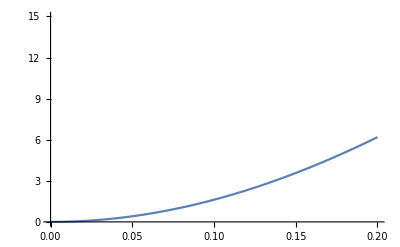

```mathematica
Plot[(pe)*100,{p,0,.2},PlotRange->{0,20}]
```

```mathematica
AD=1-Exp[-2 Pi ξ̄ Subscript[Ω, o]/Subscript[Ω̄, d]]
```

1-Abs[(36-47 p^2 π^2-2 π √(-p^2 (-36+5 p^2 π^2)^2))/((4+p^2 π^2) (9+4 p^2 π^2))]^((2 π)/ArcTan[(2 π √(p^2 (-36+5 p^2 π^2)^2))/(36-47 p^2 π^2)])

```mathematica
ξ̄=-1/Subscript[Ω, o]Log[Abs[λ1]]
```

-Log[Abs[(36-47 p^2 π^2-2 π √(-p^2 (-36+5 p^2 π^2)^2))/((4+p^2 π^2) (9+4 p^2 π^2))]]/(2 p π)

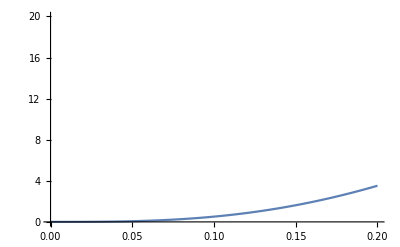

```mathematica
Plot[(AD)*100,{p,0,.2},PlotRange->{0,20}]
```

```mathematica
aNot=-({{Coefficient[Part[recursive,2],Subscript[ẋ, t]], Coefficient[Part[recursive,2],Subscript[x, t]]}, {Coefficient[Part[recursive,3],Subscript[ẋ, t]], Coefficient[Part[recursive,3],Subscript[x, t]]}})
```

{{144/((9+(4 π^2 Δt^2)/T^2) (16+(4 π^2 Δt^2)/T^2))-(188 π^2 Δt^2)/(T^2 (9+(4 π^2 Δt^2)/T^2) (16+(4 π^2 Δt^2)/T^2)),-(384 π^2 Δt)/(T^2 (9+(4 π^2 Δt^2)/T^2) (16+(4 π^2 Δt^2)/T^2))+(16 π^4 Δt^3)/(T^4 (9+(4 π^2 Δt^2)/T^2) (16+(4 π^2 Δt^2)/T^2))},{(144 Δt)/((9+(4 π^2 Δt^2)/T^2) (16+(4 π^2 Δt^2)/T^2))-(20 π^2 Δt^3)/(T^2 (9+(4 π^2 Δt^2)/T^2) (16+(4 π^2 Δt^2)/T^2)),144/((9+(4 π^2 Δt^2)/T^2) (16+(4 π^2 Δt^2)/T^2))-(76 π^2 Δt^2)/(T^2 (9+(4 π^2 Δt^2)/T^2) (16+(4 π^2 Δt^2)/T^2))}}

```mathematica
eigaNot=Eigenvalues[aNot]/.Δt->p T//Expand//Simplify//Cancel;
```

```mathematica
ppp={0,Part[eigaNot,1],Part[eigaNot,2]}
```

{0,(36 T^4-33 p^2 π^2 T^4-2 π √(-p^2 (864-205 p^2 π^2+5 p^4 π^4) T^8))/((4+p^2 π^2) (9+4 p^2 π^2) T^4),(36 T^4-33 p^2 π^2 T^4+2 π √(-p^2 (864-205 p^2 π^2+5 p^4 π^4) T^8))/((4+p^2 π^2) (9+4 p^2 π^2) T^4)}

```mathematica
qqq=eigA
```

{0,(36 T^4-47 p^2 π^2 T^4-2 π √(-p^2 (-36+5 p^2 π^2)^2 T^8))/((4+p^2 π^2) (9+4 p^2 π^2) T^4),(36 T^4-47 p^2 π^2 T^4+2 π √(-p^2 (-36+5 p^2 π^2)^2 T^8))/((4+p^2 π^2) (9+4 p^2 π^2) T^4)}

```mathematica
ppp-qqq//Simplify
```

{0,(2 π (7 p^2 π T^4+√(-p^2 (-36+5 p^2 π^2)^2 T^8)-√(-p^2 (864-205 p^2 π^2+5 p^4 π^4) T^8)))/((4+p^2 π^2) (9+4 p^2 π^2) T^4),(2 π (7 p^2 π T^4-√(-p^2 (-36+5 p^2 π^2)^2 T^8)+√(-p^2 (864-205 p^2 π^2+5 p^4 π^4) T^8)))/((4+p^2 π^2) (9+4 p^2 π^2) T^4)}